```mathematica
ToAssoc[all_]:=Block[{result={},g, h,found,i},
Table[
found=False;
g=all[k,"graph"];
For[i=1,i≤Length[result],i++,
h=all[First[result[[i]]],"graph"];
If[IsomorphicGraphQ[g,h],
AppendTo[result[[i]],k];
found=True;
i=Length[all]+1
]
];
If[!found,AppendTo[result,{k}]]
,{k,Keys[all]}
];
result
]
```

```mathematica
TableForm[ToAssoc[Select[allGraphs5,TreeGraphQ[#["graph"]]&& VertexCount[#["graph"]]==5&]],TableDepth->1]
```

{29160,20034,6816,2278,760}
{28458,28434,28432,27054,26982,26974,26352,26256,22842,22608,22602,22140,21880,20736,20416,20010,20008,19962,19954,19938,19800,19794,19774,19714,9720,9558,9504,8994,8830,7542,7318,6912,6888,6840,6814,6808,6654,6652,6600,6592,3006,2946,2538,2512,2442,2440,2304,2280,2272,2224,2218,1080,1000,984,976,840,820,814,768,766}
{26328,26326,26280,26272,26254,26248,22116,22114,21906,21900,21882,21874,20664,20656,20502,20496,20424,20422,19936,19930,19776,19768,19722,19720,9018,8992,8856,8832,8778,8776,7614,7534,7398,7380,7372,7326,6886,6832,6678,6672,6646,6598,3240,3186,3168,3162,3000,2952,2514,2466,2458,2434,2298,2226,1056,1054,1008,982,846,822}

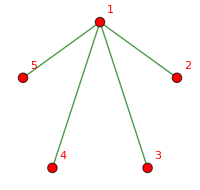
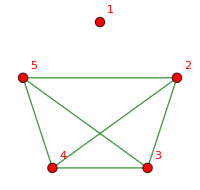
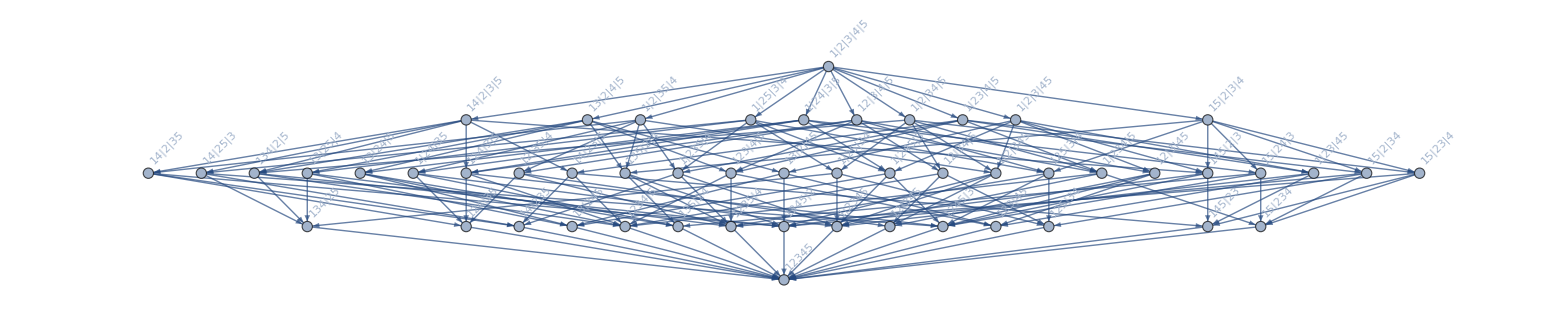
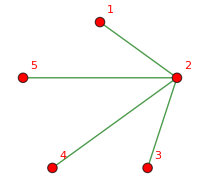
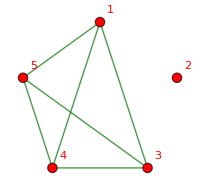
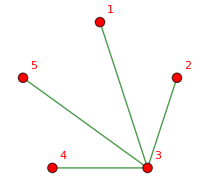
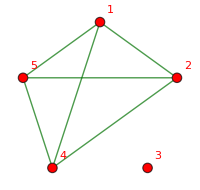
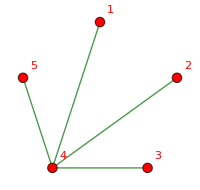
{-Graphics-29160 | -Graphics-364
-Graphics-
-Graphics-n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5+n145x2x3-n14x2x3x5-n15x2x3x4+n1x2x3x4x5x^5-4 x^4+6 x^3-4 x^2+x
(x-1)^4 x
 *  * 02483241280
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-20034 | -Graphics-9490
-Graphics-
-Graphics-n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5x^5-4 x^4+6 x^3-4 x^2+x
(x-1)^4 x
 *  * 02483241280
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-6816 | -Graphics-22708
-Graphics-
-Graphics-n12345-n1234x5-n1235x4+n123x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5x^5-4 x^4+6 x^3-4 x^2+x
(x-1)^4 x
 *  * 02483241280
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-2278 | -Graphics-27246
-Graphics-
-Graphics-n12345-n1234x5-n1245x3+n124x3x5-n1345x2+n134x2x5+n145x2x3-n14x2x3x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5x^5-4 x^4+6 x^3-4 x^2+x
(x-1)^4 x
 *  * 02483241280
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-760 | -Graphics-28764
-Graphics-
-Graphics-n12345-n1235x4-n1245x3+n125x3x4-n1345x2+n135x2x4+n145x2x3-n15x2x3x4-n1x2345+n1x235x4+n1x245x3-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5x^5-4 x^4+6 x^3-4 x^2+x
(x-1)^4 x
 *  * 02483241280
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}

```mathematica
Table[SummaryPrintGood5[k],{k,{29160,20034,6816,2278,760}}]
```